# Geodesics in Schwarzschild metric

## using Black Hole Perturbation Toolkit

Md Arif Shaikh, Postdoc, ICTS-TIFR

March 19, 2021

## Load the metric

There are built-in metric for most of the well known metrics but one can also manually set any metric. For working in Schwarzschild metric we need to do the following

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
g = ToMetric["Schwarzschild"]
```

g_αβ^

Then one can view the metric elements using TensorValues

```mathematica
g//TensorValues//MatrixForm
```

(-1+(2 M)/r | 0 | 0 | 0
0 | 1/(1-(2 M)/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

And access the metric elements

```mathematica
g[-t,-t]
```

-1+(2 M)/r

Metric can also be set in the following way

```mathematica
k = ToMetric[{"my-metric", "k"}, {t, r, θ, ϕ}, DiagonalMatrix[{-(1-(2M)/r), 1/(1-(2M)/r), r^2,r^2 Sin[θ]^2}], "Greek"]
```

k_αβ^

```mathematica
k//TensorValues//MatrixForm
```

(-1+(2 M)/r | 0 | 0 | 0
0 | 1/(1-(2 M)/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

We get the same metric as the built-in one.

## Christoffel Symbols, Riemann Tensor, Ricci Tensor and Ricci Scalar

Once we have our metric we can easily compute the other qualities using built-in functions

```mathematica
Gammas = ChristoffelSymbol[g, ActWith-> Simplify]
```

Γ_βγ^α

```mathematica
Gammas//TensorValues
```

{{{0,-M/(2 M r-r^2),0,0},{-M/(2 M r-r^2),0,0,0},{0,0,0,0},{0,0,0,0}},{{(M (-2 M+r))/r^3,0,0,0},{0,M/(2 M r-r^2),0,0},{0,0,2 M-r,0},{0,0,0,(2 M-r) Sin[θ]^2}},{{0,0,0,0},{0,0,1/r,0},{0,1/r,0,0},{0,0,0,-Cos[θ] Sin[θ]}},{{0,0,0,0},{0,0,0,1/r},{0,0,0,Cot[θ]},{0,1/r,Cot[θ],0}}}

```mathematica
Gammas[t, t, r]
```

-(M (1-(2 M)/r) r)/((2 M-r) (2 M r-r^2))

```mathematica
Riemann = RiemannTensor[g, ActWith-> Simplify]
```

R_αβγδ^

```mathematica
Riemann//TensorValues
```

{{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,-(2 M)/r^3,0,0},{(2 M)/r^3,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,(M (-2 M+r))/r^2,0},{0,0,0,0},{-(M (-2 M+r))/r^2,0,0,0},{0,0,0,0}},{{0,0,0,-(M (2 M-r) Sin[θ]^2)/r^2},{0,0,0,0},{0,0,0,0},{(M (2 M-r) Sin[θ]^2)/r^2,0,0,0}}},{{{0,(2 M)/r^3,0,0},{-(2 M)/r^3,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,M/(2 M-r),0},{0,-M/(2 M-r),0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,(M Sin[θ]^2)/(2 M-r)},{0,0,0,0},{0,-(M Sin[θ]^2)/(2 M-r),0,0}}},{{{0,0,-(M (-2 M+r))/r^2,0},{0,0,0,0},{(M (-2 M+r))/r^2,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,-M/(2 M-r),0},{0,M/(2 M-r),0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,2 M r Sin[θ]^2},{0,0,-2 M r Sin[θ]^2,0}}},{{{0,0,0,(M (2 M-r) Sin[θ]^2)/r^2},{0,0,0,0},{0,0,0,0},{-(M (2 M-r) Sin[θ]^2)/r^2,0,0,0}},{{0,0,0,0},{0,0,0,-(M Sin[θ]^2)/(2 M-r)},{0,0,0,0},{0,(M Sin[θ]^2)/(2 M-r),0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,-2 M r Sin[θ]^2},{0,0,2 M r Sin[θ]^2,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}

```mathematica
Riemann[t,-r,-t,-r]
```

-(2 M)/((2 M-r) r^2)

```mathematica
Ricci = RicciTensor[g, ActWith-> Simplify]
```

R_βγ^

```mathematica
Ricci//TensorValues
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
RS = RicciScalar[g, ActWith-> Simplify]
```

R

```mathematica
RS//TensorValues
```

0

## Set up Geodesic Equation using Christoffel Symbols

We can now set up the Geodesic Equations. First we set the four-velocity tensor

```mathematica
u = ToTensor["four-velocity", g, {vt[τ], vr[τ], vθ[τ], vϕ[τ]}]
```

(four-velocity)_^α

```mathematica
geodesicEq= D[TensorValues[u[α]],τ]+ TensorValues[ContractIndices[Gammas[α,-μ,-ν]u[μ]u[ν]]]
```

{-(2 M vr[τ] vt[τ])/(2 M r-r^2)+vt'[τ],(M vr[τ]^2)/(2 M r-r^2)+(M (-2 M+r) vt[τ]^2)/r^3+(2 M-r) vθ[τ]^2+(2 M-r) Sin[θ]^2 vϕ[τ]^2+vr'[τ],(2 vr[τ] vθ[τ])/r-Cos[θ] Sin[θ] vϕ[τ]^2+vθ'[τ],(2 vr[τ] vϕ[τ])/r+2 Cot[θ] vθ[τ] vϕ[τ]+vϕ'[τ]}

t-component is then given by

```mathematica
geodesicEq[[1]]
```

-(2 M vr[τ] vt[τ])/(2 M r-r^2)+vt'[τ]

r-component could be obtained using

```mathematica
geodesicEq[[2]]
```

(M vr[τ]^2)/(2 M r-r^2)+(M (-2 M+r) vt[τ]^2)/r^3+(2 M-r) vθ[τ]^2+(2 M-r) Sin[θ]^2 vϕ[τ]^2+vr'[τ]

and so on

## Radial equation using Conserved quantities

In practice we don’t need to start with setting up the geodesic equations to get the radial equation. In fact it is easier to start with conserved quantities, Energy and the Angular momentum and the normalization condition to set and solve the radial equation. We can get the conserved quantities using the two killing vectors

```mathematica
ξt= ToTensor["t-killing", g, {1, 0, 0, 0}]
```

(t-killing)_^α

```mathematica
ξϕ = ToTensor["phi-killing", g, {0,0,0,1}]
```

(phi-killing)_^α

```mathematica
ContractIndices[ξt[-μ]u[μ]]//TensorValues
```

(-1+(2 M)/r) vt[τ]

```mathematica
ContractIndices[ξϕ[-μ]u[μ]]//TensorValues
```

r^2 Sin[θ]^2 vϕ[τ]

```mathematica
norm = ContractIndices[u[-μ]u[μ]]//TensorValues
```

vr[τ]^2/(1-(2 M)/r)+(-1+(2 M)/r) vt[τ]^2+r^2 vθ[τ]^2+r^2 Sin[θ]^2 vϕ[τ]^2

From the θ component of the geodesic equation we get

```mathematica
θEq = geodesicEq[[3]]
```

(2 vr[τ] vθ[τ])/r-Cos[θ] Sin[θ] vϕ[τ]^2+vθ'[τ]

Let' s consider equatorial motion, i.e., θ=π/2

```mathematica
θEqEquatorial = θEq/.{θ-> π/2}
```

(2 vr[τ] vθ[τ])/r+vθ'[τ]

Now if we take the initial vθ = 0, then we get

```mathematica
θEqEquatorial/.{vθ[τ]-> 0}
```

vθ'[τ]

Which implies that the derivative of vθ also goes to zero and hence θ does not change and remains π/2. We use this in the norm expression to get

```mathematica
normEq = norm/.{θ-> π/2, vθ[τ]-> 0}
```

vr[τ]^2/(1-(2 M)/r)+(-1+(2 M)/r) vt[τ]^2+r^2 vϕ[τ]^2

We now replace the vϕ and vt using the conserved quantities

```mathematica
normEqnew = normEq/.{vt[τ]-> EE/(1-(2M)/r), vϕ[τ]-> L/r^2}
```

(EE^2 (-1+(2 M)/r))/(1-(2 M)/r)^2+L^2/r^2+vr[τ]^2/(1-(2 M)/r)

```mathematica
normCond = (normEqnew + 1)/.{EE^2-> 2Enew + 1}//Simplify
```

L^2/r^2-(2 (M+Enew r))/(-2 M+r)+(r vr[τ]^2)/(-2 M+r)

From the above Expression one can obtain the equation for vr in terms of the Energy and the angular momentum.

## Effective potential

```mathematica
Eng = Solve[normCond==0,Enew]//Values//Flatten
```

{(-2 L^2 M+L^2 r-2 M r^2+r^3 vr[τ]^2)/(2 r^3)}

```mathematica
Veff = Eng[[1]] - 1/2 vr[τ]^2//Simplify
```

(-2 M r^2+L^2 (-2 M+r))/(2 r^3)

## Plot Effective Potential vs radius

```mathematica
Veffnew = Veff/.{r-> r M, L-> λ M}//Simplify
```

(-2 r^2-2 λ^2+r λ^2)/(2 r^3)

{5,4.2,2 √3,3}

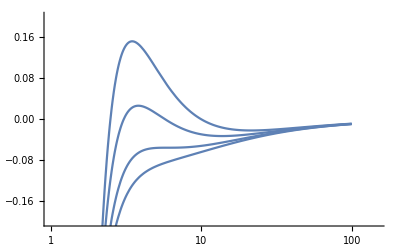

```mathematica
Lvals = {5, 4.2, 2 Sqrt[3], 3}
Show[Table[LogLinearPlot[Veffnew/.{λ-> Lvals[[idx]]}, {r, 0, 100}],{idx, 1, Length@Lvals}], PlotRange-> {{0, 5},{-0.2, 0.2}} ]
```

## ISCO

The inner most stable circular orbit (ISCO) is located at a place where Veff has a  point of inflection. Thus we find where the first derivative of Veff is zero and second derivative is also zero.

```mathematica
Vdash = D[Veffnew, r]//Simplify
```

(r^2+3 λ^2-r λ^2)/r^4

```mathematica
Vddash = D[Vdash, r]//Simplify
```

(-2 r^2-12 λ^2+3 r λ^2)/r^5

```mathematica
Solve[{Vdash==0, Vddash==0},{r, λ}]
```

{{r→6,λ→-2 √3},{r→6,λ→2 √3}}